# CS298 - HMW 1

## Kyle Perra - 7/9/2015

## Plotting:

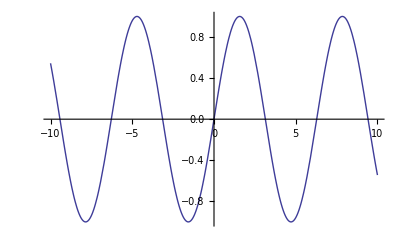

```mathematica
Plot[Sin[x],{x,-10,10}]
```

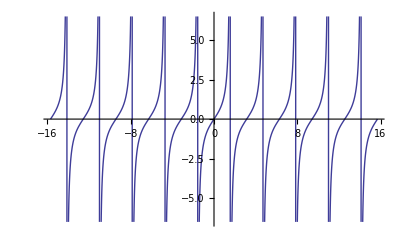

```mathematica
Plot[Tan[x],{x,-5Pi,5Pi}]
```

```mathematica
f[x_,y_]:=x^2-y^3
```

```mathematica
Plot3D[f[x,y],{x,-5,5},{y,.5,12.3}]
```

-Graphics3D-

## Truncation Errors

### Calc “true” value of cos(2) to 10 decimal places

```mathematica
Do[Print[N[result1 =Cos[2]]]]
```

-0.416147

```mathematica
SetPrecision[result1,10]
```

-0.416146837

### Calc approx. for cos(2), using first 5 terms of infinite series

```mathematica
Do[Print[N[result2 = 1-2^2/Factorial[2]+2^4/Factorial[4]+2^6/Factorial[6]+2^8/Factorial[8]]]]
```

-0.238095

### Calc absolute error for “true” and approx. values of cos(2)

```mathematica
Do[Print[N[result3=result2-result1]]]
```

0.178052

### Calc relative error for “true” and approx. values of cos(2)

```mathematica
Do[Print[N[result4=(result2-result1)/result1]]]
```

-0.427858

## Plotting and Manipulate

```mathematica
f[x_,y_]:=Sin[x^4]-Cos[12x^y]+0.7x
```

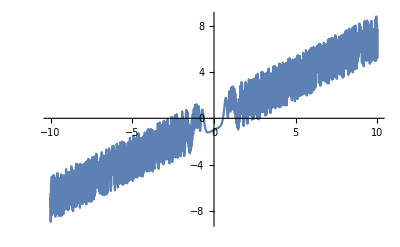

```mathematica
Plot[f[x,4],{x,-10,10}]
```

```mathematica
Manipulate[Plot[f[x,y],{x,-10,10}],{y,-10,10,1,Appearance->"Labeled"}]
```

Is there a value of y in the range {-10,10} so that the value of f(x,y) is positive, even when x is negative?
The manipulate plot suggests that yes - there are several values of y for which f{x,y) is positive, particulary when x is equal to negative one.